```mathematica
(* HARMONICKÝ USTÁLENÝ STAV *)
```

```mathematica
ClearAll["Global`*"]
(* Jak Mathematica vnímá komplexní čísla  - komplexní jednotku*)
kc1 = 10+10*ⅈ (* ESC + i + i + ESC *)
kc2 = 10+10*I (* Velké i *)
kc3 = 10+10*ⅉ (* ESC + j + j + ESC *)
kc4 = 1-ⅉ

kc1==kc2==kc3
kc1==kc2==kc3==kc4

I
ⅈ
ⅉ
```

10+10 ⅈ

10+10 ⅈ

10+10 ⅈ

1-ⅈ

True

False

ⅈ

ⅈ

ⅈ

```mathematica
ClearAll["Global`*"]
(* Tvary komplexního čísla *)
z1 = a+ⅉ*b (* algebraický tvar *)
z2 = Abs[z]*(Cos[φ]+ⅉ*Sin[φ]) (* goniometrický tvar *)
Cos[φ]+ⅉ*Sin[φ] == ⅇ^(ⅉ*φ) (* Eulerův vztah *)
z3 = Umax*ⅇ^(ⅉ*φ)
```

a+ⅈ b

Abs[z] (Cos[φ]+ⅈ Sin[φ])

Cos[φ]+ⅈ Sin[φ]==ⅇ^(ⅈ φ)

ⅇ^(ⅈ φ) Umax

```mathematica
ClearAll["Global`*"]
(* Operace pro práci s kompelxními čísly *)
z1 = a+ⅉ*b;
z1 = 12.8-14.7ⅉ;
Re[z1] (* reálná část *)
Im[z1] (* imaginární část *)

z2 = 14.-8ⅈ;
z3 = 5+9I;
z4 = z1+z2+z3;

Abs[z2]
Arg[z2]

absolutniHodnotaZ2 = √(Re[z2]^2+Im[z2]^2)
```

12.8

-14.7

16.1245

-0.519146

16.1245

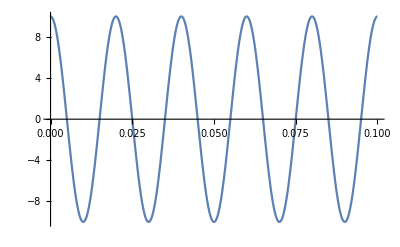

```mathematica
ClearAll["Global`*"]
amplitudaU = 10;
f = 50;
ω = 2*π*f;
perioda = 1/f;
tmax = 5*perioda;
φ = π/2;
u[t_]:=amplitudaU*Sin[ω*t+φ]
Plot[u[t],{t,0,tmax}]
```

```mathematica
ClearAll["Global`*"]
(* Fázor  - komplexní číslo *)

Uf = Umax*ⅇ^(ⅉ*φ);

(* PŘÍKLAD 1 *)
Uf1 = 12.+7*ⅉ;
Umax1 = Abs[Uf1] (* V *)
φ1 = Arg[Uf1]

u[t]= Umax1*Sin[ω*t+φ1]
Uf = Umax1*ⅇ^(ⅉ*ω*t)*ⅇ^(ⅉ*φ1)

(* φ - ESC + j + ESC *)
(* ⅉ - ESC + j+j + ESC *) 
(* ⅇ - ESC + e+e + ESC *)
```

13.8924

0.528074

```mathematica
(* PŘÍKLAD 2*)
ClearAll["Global`*"]
Umax2 = 15;
φ2 = π/3;

Uf = Umax2*ⅇ^(ⅉ*φ2)
Uf//N
```

15 ⅇ^((ⅈ π)/3)

7.5+12.9904 ⅈ

```mathematica
(* PŘÍKLAD 3*)
ClearAll["Global`*"]
u[t] =9.2*Sin[100*t+2.4]

Uf3 = 9.2*ⅇ^(ⅉ*2.4)
ω3 = 100
f = 100./(2*π)
```

9.2 Sin[2.4+100 t]

-6.78402+6.21426 ⅈ

100

15.9155

13.8159

0.385883

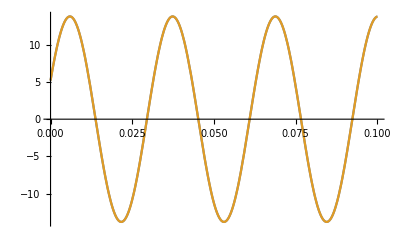

```mathematica
(* PŘÍKLAD 4*)
ClearAll["Global`*"]
Uf4 = 12.8+5.2ⅉ;

ω4 = 200;
Umax4 = Abs[Uf4]
φ4 = Arg[Uf4]

uZ = Umax4*ⅇ^(ⅉ*φ4)



u4[t_]:=Umax4*Sin[ω4*t+φ4]
u4f[t_]:=Im[Uf4 *ⅇ^(ⅉ*ω4*t)]

Plot[{u4[t], u4f[t]},{t,0,0.1}]
```

```mathematica
(*vysvětlení příkladu výše*)
ⅇ^(ⅉ*x)== Cos[x]+ ⅉ*Sin[x]
Umax*ⅇ^(ⅉ*(ω*t+φ)) ==Umax*Cos[ω*t+φ]+ ⅉ*Umax*Sin[ω*t+φ]
Im[Umax*ⅇ^(ⅉ*(ω*t+φ))]==Umax*Sin[ω*t+φ]
Im[Umax*ⅇ^(ⅉ*ω*t)*ⅇ^(ⅉ*φ)]==Umax*Sin[ω*t+φ]
Im[Umax*ⅇ^(ⅉ*φ)*ⅇ^(ⅉ*ω*t)]==Umax*Sin[ω*t+φ]
```